```mathematica
G := SetPrecision[6.674*10^(-8), 80] (*en cgs*)
c := SetPrecision[2.998*10^(10), 80](*en cgs*)
ti :=SetPrecision[ 1.48*10^(12), 80](*s*)
ρt :=SetPrecision[ 100, 80] (*cgs *)
```

```mathematica
ηi := 2.96*10^(12)
```

```mathematica
func[x_]:= 1/2*ηi/(x*(1+x^2)^(1/2))*(ArcSinh[x]+x √(1+x^2)) - ti
```

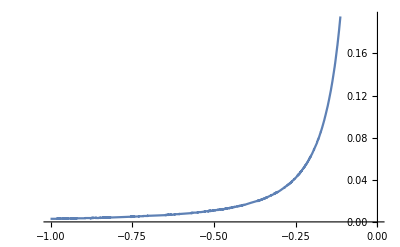

```mathematica
Plot[func[x], {x, -10^8, 0}]
```

```mathematica
Limit[func[x], {x-> ∞}]
```

0.

```mathematica
Limit[func[x], {x-> -∞}]
```

0.

```mathematica
Plot[ArcSinh[x]+x √(1+x^2), {x, -10^8,10^8}]
```

-Graphics-